```mathematica
ResourceFunction["AddStyleToNotebook"][EvaluationNotebook[],"Input",{Background -> LightBlue}];
ResourceFunction["AddStyleToNotebook"][EvaluationNotebook[],"Output",{Background -> LightOrange}];
SetOptions[EvaluationNotebook[], Background -> LightGreen]
```

```mathematica
cleanJsonFull = Import["cleanedFile_KyanaBurhite.json"];
```

```mathematica
cleanJsonFull[RandomSample[cleanJsonFull]];
```

```mathematica
106316.4
```

```mathematica
cleanJson = cleanJsonFull[[;;106316, All]];
cleanJsonTest= cleanJsonFull[[106316;;All]];
```

```mathematica
{106316,3}
```

```mathematica
{5597,3}
```

```mathematica
featureTrain = FeatureExtraction[{"WordVectors"}]
```

```mathematica
classifier = Classify[cleanJson[[All, ;;2]] -> cleanJson[[All, 3]] ,TrainingProgressReporting->"Print"]
```

```mathematica
classifier = Classify[cleanJson[[All, ;;2]] -> cleanJson[[All, 3]], Method->{"NeuralNetwork"}, TrainingProgressReporting->"Panel"]
```

```mathematica
ClassifierFunction[…]
```

```mathematica
resultHopeful = cleanJsonTest[[All, 3]];
tests = cleanJsonTest[[All, 1;;2]];
```

```mathematica
wallus = classifier[#]&/@tests;
```

```mathematica
hypothesis = Values[resultHopeful];
```

```mathematica
result = Values[wallus];
```

```mathematica
{5597}
```

```mathematica
allTest = If[hypothesis[[#]] != result[[#]], hypothesis[[#]]- result[[#]], Unevaluated[Sequence[]]]&/@Range[5597];
```

```mathematica
Length[If[allTest[[#]] <= -1, #, Unevaluated[Sequence[]]]&/@Range[Length[allTest]]]
Length[If[allTest[[#]] >= 1, #, Unevaluated[Sequence[]]]&/@Range[Length[allTest]]]
allTest
```

```mathematica
classed = ClassifierMeasurements[classifier, cleanJsonTest[[All, ;;2]]  -> cleanJsonTest[[All, 3]] ];
classed
```

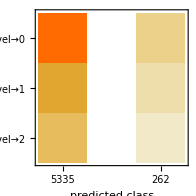
```mathematica
{{"Classifier Measurements"}, {{{Classifier method, NeuralNetwork}, {Number of test examples, 5597}, {Accuracy, Quantity[(69.40.6), "Percent"]}, {Accuracy baseline, Quantity[(72.10.6), "Percent"]}, {Geometric mean of probabilities, 0.3697321019320209956`3." ± "0.0027154829855440266`2.}, {Mean cross entropy, 0.9949765844261939662`3." ± "0.0073443949260942332`2.}, {Single evaluation time, Quantity[50.8, ("Milliseconds")/("Examples")]}, {Batch evaluation speed, Quantity[9.52, ("Examples")/("Milliseconds")]}, {-Graphics-, }}}}
```

```mathematica
classed["ConfusionMatrixPlot"]
```